```mathematica
MatrizElement[el_,NE_]:=Block[{KE,FE,xa,xb,phiem1,phie},
KE=Table[0,{2},{2}];
FE=Table[0,{2}];
xa=(el-1)/NE;
xb=el/NE;
phiem1[x_]=(xb-x)/(xb-xa);
phie[x_]=(x-xa)/(xb-xa);
KE[[1,1]]=Integrate[D[phiem1[x],x]^2+phiem1[x]^2,{x,xa,xb}];
KE[[1,2]]=Integrate[D[phiem1[x],x]D[phie[x],x]+phiem1[x]phie[x],{x,xa,xb}];
KE[[2,1]]=KE[[1,2]];
KE[[2,2]]=Integrate[D[phie[x],x]^2+phie[x]^2,{x,xa,xb}];
FE[[1]]=Integrate[phiem1[x]x,{x,xa,xb}];
FE[[2]]=Integrate[phie[x]x,{x,xa,xb}];
{KE,FE}
]
Assemble[el_,NE_,KElemento_,KGlobal_]:=Block[{KMatriz,KVetor,KMatrizGlobal,KVetorGlobal},
KMatrizGlobal=KGlobal[[1]];
KVetorGlobal=KGlobal[[2]];
KMatriz=KElemento[[1]];
KVetor=KElemento[[2]];

index=el;
If[el==1,
KMatrizGlobal[[1,1]]+=KMatriz[[2,2]];
KVetorGlobal[[1]]+=KVetor[[2]],

If[el==NE,
KMatrizGlobal[[NE-1,NE-1]]+=KMatriz[[1,1]];
KVetorGlobal[[NE-1]]+=KVetor[[1]]
,
KMatrizGlobal[[el-1,el-1]]+=KMatriz[[1,1]];
KMatrizGlobal[[el-1,el]]+=KMatriz[[1,2]];
KMatrizGlobal[[el,el-1]]+=KMatriz[[2,1]];
KMatrizGlobal[[el,el]]+=KMatriz[[2,2]];
KVetorGlobal[[el-1]]+=KVetor[[1]];
KVetorGlobal[[el]]+=KVetor[[2]]
]
];
{KMatrizGlobal,KVetorGlobal}
]
```

```mathematica
{K,F}=MatrizElement[1,1/h];
K//MatrixForm
F//MatrixForm
```

(1/h+h/3 | -1/h+h/6
-1/h+h/6 | 1/h+h/3)

(h^2/6
h^2/3)

```mathematica
NElementos=10
TodosErros={};
TodosErrosL2={};
For[NElementos=2,NElementos≤128,NElementos*=2,
KGlobal={
Table[0,{NElementos-1},{NElementos-1}],
Table[0,{NElementos-1}]
};
For[el=1,el≤NElementos,el++,
KElem=MatrizElement[el,NElementos]//Simplify;
KGlobal=Assemble[el,NElementos,KElem,KGlobal]
];
alfa=LinearSolve[KGlobal[[1]],KGlobal[[2]]]//N;

xalfa=Table[{i 1./NElementos,alfa[[i]]},{i,1,NElementos-1}];
PrependTo[xalfa,{0,0}];
AppendTo[xalfa,{1,0}];
func=Interpolation[xalfa,InterpolationOrder->1];
exata[x_]=x /1-Sinh[x]/Sinh[1];
Erro[x_]=exata[x]-func[x];
DErro[x_]=D[Erro[x],x];
NormaErro=Sqrt[NIntegrate[DErro[x]^2+Erro[x]^2,{x,0,1}]];
NormaErroL2=Sqrt[NIntegrate[Erro[x]^2,{x,0,1}]];
AppendTo[TodosErros,{Log[1./NElementos],Log[NormaErro]}];
AppendTo[TodosErrosL2,{Log[1./NElementos],Log[NormaErroL2]}]
]
TodosErros
TodosErrosL2
```

10

{{-0.693147,-2.56853},{-1.38629,-3.24532},{-2.07944,-3.93448},{-2.77259,-4.62663},{-3.46574,-5.31953},{-4.15888,-6.01262},{-4.85203,-6.70576}}

{{-0.693147,-4.46784},{-1.38629,-5.83278},{-2.07944,-7.21382},{-2.77259,-8.59881},{-3.46574,-9.98478},{-4.15888,-11.371},{-4.85203,-12.7573}}

0.00122384

2.88132×10^-6

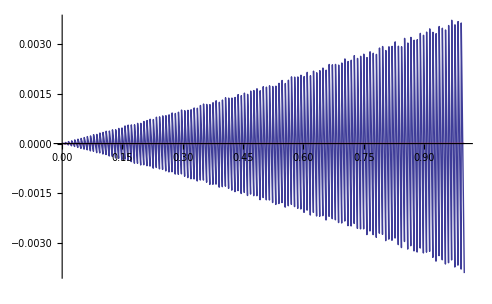

```mathematica
NormaErro
NormaErroL2
Plot[{DErro[x],Erro[x]},{x,0,1},PlotRange->All]
```

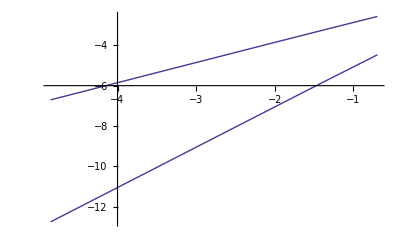

0.994795

1.99318

```mathematica
a=ListPlot[TodosErros,PlotJoined->True];
b=ListPlot[TodosErrosL2,PlotJoined->True];
Show[a,b,PlotRange->All]
(TodosErros[[-1]][[2]]-TodosErros[[1]][[2]])/(TodosErros[[-1]][[1]]-TodosErros[[1]][[1]])
(TodosErrosL2[[-1]][[2]]-TodosErrosL2[[1]][[2]])/(TodosErrosL2[[-1]][[1]]-TodosErrosL2[[1]][[1]])
```